## Initialization Notation

```mathematica
(*get association of resources,name of local host and remove local host from available resources*)hosts=Counts[ReadList[Environment["NODEFILE"],"String"]]
local=First[StringSplit[Environment["HOSTNAME"],"."]]
hosts[local]--;
(*launch subkernels and connect them to the controlling Wolfram Kernel*)
Needs["SubKernels`RemoteKernels`"];
Map[If[hosts[#]>0,LaunchKernels[RemoteMachine[#,"ssh -x -f -l `3` `1` /gpfs/runtime/opt/mathematica/12.0/Executables/wolfram -wstp -linkmode Connect `4` -linkname '`2`' -subkernel -noinit",hosts[#]]]]&,Keys[hosts]];
dir=DirectoryName[$InputFileName];
```

```mathematica
Unprotect[Out];
$HistoryLength=0;
ParallelEvaluate[$HistoryLength=0];
<<NDSolve`FEM`
(*dir=NotebookDirectory[]
SetDirectory[dir]*)
```

```mathematica
ClearAll[PlotMeshBC]
Protect[ShowMesh,ShowNumbers,ShowBCs];
Options[PlotMeshBC]={ShowMesh->False,ShowNumbers->False,ShowBCs->False};
PlotMeshBC[DirichletPoints_,NeumannPoints_,OptionsPattern[]]:=
If[OptionValue[ShowMesh],
Block[{PltPoints,plt},
Switch[OptionValue[ShowBCs]
,"DirichletBC"
,PltPoints =Cases[DirichletPoints,{#,_}][[;;,2]]&/@Range[ndof];
plt = True;
,"NeumannBC"
,PltPoints =Cases[NeumannPoints,{#,_}][[;;,2]]&/@Range[ndof];
plt = True;
,False
,plt =False;];
Show[
Join[{mesh["Wireframe"]}
,
If[OptionValue[ShowNumbers]
,{mesh["Wireframe"["MeshElement" -> "MeshElements","MeshElementIDStyle"->Blue]]
,mesh["Wireframe"["MeshElement" -> "PointElements","MeshElementIDStyle"->Red]]},{}]
,
If[plt
,Switch[ndof
,2,{Graphics[{PointSize[Large],Orange,Point[Coords[[PltPoints[[1]]]]]}]
,Graphics[{PointSize[Large],Green,Point[Coords[[PltPoints[[2]]]]]}]}
,3,{Graphics3D[{PointSize[Large],Orange,Point[Coords[[PltPoints[[1]]]]]}]
,Graphics3D[{PointSize[Large],Green,Point[Coords[[PltPoints[[2]]]]]}]
,Graphics3D[{PointSize[Large],Purple,Opacity[0.3],Point[Coords[[PltPoints[[3]]]]]}]}
],{}]
]]],Null];

PrintBB[X_List]:=Block[{},
Print[Sequence@@(Style[#,Blue,Bold]&/@X)];
]
PrintRB[X_List]:=Block[{},
Print[Sequence@@(Style[#,Red,Bold]&/@X)];
]
```

## Problem Solution: Numerics

### Numerics subroutine:

```mathematica
ClearAll[DefineBCs];
DefineBCs[uVec_,tVec_,L_,CrackLen_]:=
Block[{tol=10^-5,IDArray},
DirichletPoints=Block[{Bttm,BttmRit,Rit,RitBttm,Tp,Nodes},
Bttm =Flatten@Position[Abs[Coords[[;;,2]]-0.0],x_/;x<tol];
BttmRit= Position[Coords[[Bttm,1]]-CrackLen,x_/;x≥tol];
Rit= Flatten@Position[Abs[Coords[[;;,1]]-L],x_/;x<tol];
RitBttm= Position[Abs[Coords[[Rit,2]]-0.0],x_/;x<tol];
Tp= Flatten@Position[Abs[Coords[[;;,2]]-L],x_/;x<tol];
If[Norm@Through[tVec[1,1,1]]<tol,
Nodes = Join[{1,#}&/@Extract[Rit,RitBttm],{2,#}&/@Extract[Bttm,BttmRit],{2,#}&/@Tp]
,Nodes = Join[{1,#}&/@Extract[Rit,RitBttm],{2,#}&/@Extract[Bttm,BttmRit]]
]
];
DirichletDof = Sort[(DirichletPoints[[;;,2]]-1)*ndof+DirichletPoints[[;;,1]]];
NeumannPoints=Block[{Tp,Nodes},
Tp=Flatten@Position[Abs[Coords[[;;,2]]-L],x_/;x<tol];
Nodes =  {2,#}&/@Tp
];
NeumannDof= Sort[(NeumannPoints[[;;,2]]-1)*ndof+NeumannPoints[[;;,1]]];
Edges =Extract[mesh["BoundaryElements"][[1,1]],Position[Map[Norm@(#-{0,1})&,mesh["BoundaryNormals"][[1]]],x_/;x<tol]];
DirichletVals=uVec[[#[[1]]]][Coords[[#[[2]]]]]&/@DirichletPoints;
NeumannVals=tVec[[#[[1]]]][Coords[[#[[2]]]]]&/@NeumannPoints;
IDArray=Range[ndof*nnp];
IDMat=Transpose[ArrayReshape[IDArray,{nnp,ndof}]];
IDno=Complement[IDArray,DirichletDof];
]
```

```mathematica
DefineGaussAndSFInfo[ElementType_,integrationOrder_,elementOrder_]:=
Block[{},
GuassPointsNatural=ElementIntegrationPoints[ToExpression[ElementType],integrationOrder];
GaussIndex=AssociationMap[Position[GuassPointsNatural,#][[1,1]]&,GuassPointsNatural];
GuassWeights=ElementIntegrationWeights[ToExpression[ElementType],integrationOrder];
NMat=ElementShapeFunction[ToExpression[ElementType],elementOrder];
dN= ElementShapeFunctionDerivative[ToExpression[ElementType],elementOrder];
];
GuassIntegrate[coord_List,f0_]:=
Block[{f=f0,GuassPointsSpatial},
GuassPointsSpatial=Apply[NMat,GuassPointsNatural,2].coord;
GuassWeights.MapThread[f,{GuassPointsNatural,GuassPointsSpatial}]
];
```

```mathematica
stress[e0_,dt_,BMat:_,ELEdu:_,ElTypId_,ξ_List]:=
Block[
{e=e0,gi,dϵ,de,S,σequiv,solϵp,Δϵplas,β,Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ},
{Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ}=MaterialProperty;
gi=GaussIndex@ξ;
dϵ=ConstantArray[0.0,{3,3}];
dϵ[[;;ndof,;;ndof]]=((BMat[ξ].ELEdu)+Transpose[(BMat[ξ].ELEdu)])/2;
de=(dϵ-Tr[dϵ]/3 IdentityMatrix[3]);
S =(σ[[ElTypId,e,gi]]-Tr[σ[[ElTypId,e,gi]]]/3 IdentityMatrix[3])+Ε/(1+ν)de;
σequiv=Sqrt[3./2.]Norm[S,"Frobenius"];
ClearAll[x];
solϵp=NSolve[σequiv/Y-(3Ε)/(2 Y (1+ν)) x-(1+(ϵplas[[ElTypId,e,gi]]+x)/ϵ0)^(1./𝓃)(x/(dt ϵdot0 (*Exp[-Q/k T]*)))^(1./𝓂)==0&&x≥0,x,Reals];
Δϵplas=x/.solϵp[[1]];
β=If[σequiv>0,1-(3 Ε Δϵplas)/(2(1+ν)σequiv),1.0];
β S+(Tr[σ[[ElTypId,e,gi]]]/3+Κ Tr[dϵ]) IdentityMatrix[3]
]

Tangent[e0_,dt_,BMat:_,ELEdu:_,ElTypId_,ξ_List]:=
Block[{e=e0,gi,dϵ,de,S,σequiv,solϵp,Δϵplas,ϵplasNew,β,σnew,γ,factor,Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ},
{Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ}=MaterialProperty;
gi=GaussIndex@ξ;
dϵ=ConstantArray[0.0,{3,3}];
dϵ[[;;ndof,;;ndof]]=((BMat[ξ].ELEdu)+Transpose[(BMat[ξ].ELEdu)])/2;
de=(dϵ-Tr[dϵ]/3 IdentityMatrix[3]);
S =(σ[[ElTypId,e,gi]]-Tr[σ[[ElTypId,e,gi]]]/3 IdentityMatrix[3])+Ε/(1+ν)de;
σequiv=Sqrt[3./2.]Norm[S,"Frobenius"];
ClearAll[x];
solϵp=NSolve[σequiv/Y-(3Ε)/(2 Y (1+ν)) x-(1+(ϵplas[[ElTypId,e,gi]]+x)/ϵ0)^(1./𝓃)(x/(dt ϵdot0 (*Exp[-Q/k T]*)))^(1./𝓂)==0&&x≥0,x,Reals];
Δϵplas=x/.solϵp[[1]];
ϵplasNew=ϵplas[[ElTypId,e,gi]]+ Δϵplas;
β=If[σequiv>0,1-(3 Ε Δϵplas)/(2(1+ν)σequiv),1.0];
σnew=β S+(Tr[σ[[ElTypId,e,gi]]]/3+Κ Tr[dϵ]) IdentityMatrix[3];
S=(σnew-Tr[σnew]/3 IdentityMatrix[3]);
σequiv=Sqrt[3./2.]Norm[S,"Frobenius"];
If[σequiv*Δϵplas>0,β=(1+(3 Ε Δϵplas)/(2(1+ν)σequiv))^-1;γ=β((3 Ε)/(2(1+ν)σequiv)+(1/(𝓃(ϵ0+ϵplasNew))+1/(𝓂  Δϵplas)));
factor = (9.Ε(Δϵplas-1/γ))/(4.(1+ν)σequiv^3);,β=1.;factor = 0.;];
(2 β μ(𝕀0+factor S⊗S)+Κ ℐ)[[;;ndof,;;ndof,;;ndof,;;ndof]]
]
```

```mathematica
ClearAll[ComputeResidualMatrixU];
SetAttributes[ComputeResidualMatrixU,HoldFirst];
ComputeResidualMatrixU[rMat_,e0_,UMat_,dt_,ElTypId_]:=
Block[{e=e0,B,Q,jacobi,BMat,ELEf,ELEr,ELEd,ℐr,ELEu,coord},
B=IEN[[ElTypId,;;,e]];
Q=Flatten@IDMat[[;;,B]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
(*ELEf=-jacobi[#1](3 λ+2 μ) αΔT[#2]BMat[#1]&;*)
ELEr=jacobi[#]*stress[e,dt,BMat,ELEu,ElTypId,#][[;;ndof,;;ndof]].BMat[#]&;
ELEd=(*ELEf[#1,#2]*)-ELEr[#1]&;
ℐr= Flatten@GuassIntegrate[coord,ELEd];
rMat[[Q]]+=ℐr;
]


ClearAll[ComputeStiffnessMatrixU];
SetAttributes[ComputeStiffnessMatrixU,HoldFirst];
ComputeStiffnessMatrixU[KMat_,e0_,UMat_,dt_,ElTypId_]:=
Block[{e=e0
,B,Q,jacobi,BMat,ELEk,ℐk,coord,ELEu
},
B=IEN[[ElTypId,;;,e]];
Q=Flatten@IDMat[[;;,B]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
ELEk=jacobi[#]Transpose[BMat[#]].Tangent[e,dt,BMat,ELEu,ElTypId,#].BMat[#]&;
ℐk=Flatten[GuassIntegrate[coord,ELEk],{{2,1},{3,4}}];
KMat[[Q,Q]]+=ℐk;
]
```

```mathematica
ClearAll[UpdateStrainStress];
UpdateStrainStress[σ_,ϵplas_,dt_,BMat:_,ELEdu:_,ξ_List]:=
Block[{gi,dϵ,de,S,σequiv,solϵp,Δϵplas,β,γ,factor,Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ,dσ},
{Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ}=MaterialProperty;
gi=GaussIndex@ξ;
dϵ=ConstantArray[0.0,{3,3}];
dϵ[[;;ndof,;;ndof]]=((BMat[ξ].ELEdu)+Transpose[(BMat[ξ].ELEdu)])/2;
de=(dϵ-Tr[dϵ]/3 IdentityMatrix[3]);
S =(σ[[gi]]-Tr[σ[[gi]]]/3 IdentityMatrix[3])+Ε/(1+ν)de;
σequiv=Sqrt[3./2.]Norm[S,"Frobenius"];
ClearAll[x];
solϵp=NSolve[σequiv/Y-(3Ε)/(2 Y (1+ν)) x-(1+(ϵplas[[gi]]+x)/ϵ0)^(1./𝓃)(x/(dt ϵdot0 (*Exp[-Q/k T]*)))^(1./𝓂)==0&&x≥0,x,Reals];
Δϵplas=x/.solϵp[[1]];
β=If[σequiv>0,1-(3 Ε Δϵplas)/(2(1+ν)σequiv),1.0];
dσ=β S+(Tr[σ[[gi]]]/3+Κ Tr[dϵ]) IdentityMatrix[3]-σ[[gi]];
{dσ,Δϵplas}
];

ClearAll[UpdateStates];
UpdateStates[σ_,ϵplas_,e0_,wMat_,dt_,ElTypId_]:=
Block[{e=e0,B,BMat,ELEu,coord},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[wMat[[;;,B]]];
UpdateStrainStress[σ,ϵplas,dt,BMat,ELEu,#]&/@GuassPointsNatural]
```

```mathematica
CalrMat[UMat_,dt_,ElTypId_]:=Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,rMat},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
ParallelEvaluate[rMat=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ComputeResidualMatrixU[rMat,n,UMat,dt,ElTypId],{n,Range[nel[[ElTypId]]]}];
rMat=Plus@@(ParallelEvaluate@rMat);
rMat
];
CalKMat[UMat_,dt_,ElTypId_]:= 
Block[{
GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,KMat
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
ParallelEvaluate[KMat=SparseArray[{},{ndof*nnp,ndof*nnp},0.0]];
ParallelDo[ComputeStiffnessMatrixU[KMat,n,UMat,dt,ElTypId],{n,Range[nel[[ElTypId]]]}];
KMat=Plus@@(ParallelEvaluate@KMat);
(*KMat=SparseArray[{},{ndof*nnp,ndof*nnp},0.0];
Do[ComputeStiffnessMatrixU[KMat,n,UMat,dt,ElTypId],{n,Range[nel[[ElTypId]]]}];*)
KMat
]

CalState[σ_,ϵplas_,wMat_,dt_,ElTypId_]:= 
Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,dState,dσ,dϵplas},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
dState=(*Parallel*)Map[UpdateStates[σ[[#]],ϵplas[[#]],#,wMat,dt,ElTypId]&,Range[nel[[ElTypId]]]];
dσ=dState[[;;,;;,1]];
dϵplas=dState[[;;,;;,2]];
(*Print["dState",dState];
Print["dσ",dσ];
Print["σ",σ];
Print["dϵplas",dϵplas];
Print["ϵplas",ϵplas];*)
{dσ,dϵplas}
]
ParallelResidual[UMat_,dt_,TracInd_]:= 
Block[{rMat,Err,tMat},
rMat=Plus@@(CalrMat[UMat,dt,#]&/@Range@nElTyp);
If[TracInd,
ParallelEvaluate[tMat=SparseArray[{},{ndof*nnp},0.0]];
ParallelDo[ApplyTraction[tMat,edge],{edge,Edges}];
tMat=Plus@@(ParallelEvaluate@tMat);
rMat+=tMat;
];
(*If[TracInd,ApplyTraction[rMat,#]&/@Edges;];*)
Err =Norm[rMat[[IDno]],Infinity];
{Err,rMat}
]

ParallelStiffness[UMat_,dt_]:= 
Block[{KMat},
KMat=Plus@@(CalKMat[UMat,dt,#]&/@Range@nElTyp);
KMat
]

ParallelUpdateStates[σin_,ϵplasin_,wMat_,dt_]:= 
Block[{σ=σin,ϵplas=ϵplasin,dState,dσ,dϵplas},
dState=CalState[σ[[#]],ϵplas[[#]],wMat,dt,#]&/@Range[nElTyp];
dσ=dState[[;;,1]];
dϵplas=dState[[;;,2]];
(*Print["dσ",dσ];
Print["σ",σ];
Print["dϵplas",dϵplas];
Print["ϵplas",ϵplas];*)
σ+=dσ;
ϵplas+=dϵplas;
{σ,ϵplas}
]
```

```mathematica
ClearAll[ApplyTraction];
SetAttributes[ApplyTraction,HoldFirst];
ApplyTraction[rMat_,Edge_]:=
Block[{
ElementType=Head@mesh["BoundaryElements"][[1]],
elementOrder=mesh["MeshOrder"],
integrationOrder = 2
,OutEdge,coord,jacobi,ELEtMat,ELEt,Q
,GuassPointsNatural,GuassWeights,NMat,dN,NetTrctn
},
GuassPointsNatural=ElementIntegrationPoints[ElementType,integrationOrder];
GuassWeights=ElementIntegrationWeights[ElementType,integrationOrder];
NMat=ElementShapeFunction[ElementType,elementOrder];dN= ElementShapeFunctionDerivative[ElementType,elementOrder];
OutEdge=Flatten[Outer[List,Range[ndof],Edge],1];
coord =Coords[[Edge]];
jacobi =If[ndof==3,Norm[Cross@@((dN@@#).coord)]&
,Norm[(dN@@#).coord]&];
ELEtMat=ArrayReshape[ReplacePart[Map[NeumannBC,OutEdge],Position[KeyExistsQ[NeumannBC,#]&/@OutEdge,False]->0.0],{ndof,nsen}];
ELEt=jacobi[#](ELEtMat.NMat@@#)&;
NetTrctn=GuassWeights.(ELEt/@GuassPointsNatural);
Q=Flatten@IDMat[[;;,Edge]];
rMat[[Q]]+=Flatten[ConstantArray[#/nsen,nsen]&/@NetTrctn];
]
```

```mathematica
ClearAll[ComputeStressProjection];
SetAttributes[ComputeStressProjection,HoldFirst];
ComputeStressProjection[{aMat_,UdMat_},e0_,UMat_,σ_,ElTypId_]:=
Block[{e=e0,B,jacobi,BMat,ℐk,ℐf,ff,fk,coord,ELEu},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
fk=jacobi[#](NMat@@#)⊗(NMat@@#)&;
ℐk=GuassIntegrate[coord,fk];
aMat[[B,B]]+=ℐk;
ff=jacobi[#](NMat@@#)⊗Flatten[σ[[e,GaussIndex@#]]]&;
ℐf=GuassIntegrate[coord,ff];
UdMat[[B,;;]]+=ℐf;
]

CalAUdMat[UMat_,σ_,ElTypId_]:= 
Block[{
GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,aMat,UdMat
},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
ParallelEvaluate[aMat=SparseArray[{},{nnp,nnp},0.0]];
ParallelEvaluate[UdMat=ConstantArray[0.0,{nnp,9}]];
ParallelDo[ComputeStressProjection[{aMat,UdMat},n,UMat,σ,ElTypId],{n,Range[nel[[ElTypId]]]}];
aMat=Plus@@(ParallelEvaluate@aMat);
UdMat=Plus@@(ParallelEvaluate@UdMat);
{aMat,UdMat}
]

StressRecover[UMat_,σ_]:=Block[{AUdMat,aMat,UdMat,SolUd,SolUdMat,StressMat,StressMatf},
AUdMat=CalAUdMat[UMat,σ[[#]],#]&/@(Range@nElTyp);
aMat=Plus@@AUdMat[[;;,1]];
UdMat=Plus@@AUdMat[[;;,2]];
SolUd=LinearSolve[aMat,UdMat];
StressMat=ArrayReshape[SolUd,{Length@SolUd,3,3}];
StressMatf=ArrayReshape[ElementMeshInterpolation[{mesh},Flatten[StressMat,{2,3}][[#,;;]]] & /@ Range[9],{3,3}];
StressMatf
]
```

```mathematica
(*Only applicable in Linear Elastic*)
(*ComputeRF[UMat_,dt_]:=Block[{KMat,udsol,udMat,RFTotalVec,RFPos},
KMat=ParallelStiffness[];
RFTotalVec=(Flatten[UMat^ᵀ][[IDno]].KMat[[IDno,DirichletDof]]+Flatten[UMat^ᵀ][[DirichletDof]].KMat[[DirichletDof,DirichletDof]]);
RFPos= Flatten[Position[DirichletDof,#]&/@NeumannDof];
Total@RFTotalVec[[RFPos]]
];*)
ClearAll[CalEE];
CalEE[UMat_,σ_,ElTypId_]:=Block[{GuassPointsNatural,GaussIndex,GuassWeights,NMat,dN,Eg},
DefineGaussAndSFInfo[ElementType[[ElTypId]],integrationOrder,elementOrder];
ParallelEvaluate[Eg=0];
ParallelDo[ComputeEE[Eg,n,UMat,σ,ElTypId],{n,nel[[ElTypId]]}];
Plus@@(ParallelEvaluate@Eg)
]

ClearAll[ComputeEE];
SetAttributes[ComputeEE,HoldFirst];
ComputeEE[Eg_,e0_,UMat_,σ_,ElTypId_]:=
Block[{e=e0,B,coord,jacobi,BMat,ELEu,ELEσ,ELEEg},
B=IEN[[ElTypId,;;,e]];
coord=Coords[[B]];
jacobi=Det@((dN@@#).coord)&;
BMat=(Inverse[(dN@@#).coord].dN@@#)&;
ELEu=Transpose[UMat[[;;,B]]];
ELEσ=σ[[e,GaussIndex@#]][[;;ndof,;;ndof]]&;
ELEEg=jacobi[#]*Tr[ELEσ[#].(BMat[#].ELEu)]&;
Eg+=GuassIntegrate[coord,ELEEg];
]
```

```mathematica
ClearAll[InitializationUState];
SetAttributes[InitializationUState,HoldAll];
InitializationUState[wMat_,uMat_,σ_,ϵplas:_]:=Block[{},
ngauss=Length/@(ElementIntegrationWeights[#,integrationOrder]&/@ElementType);
wMat=ConstantArray[0.0,{ndof,nnp}];
uMat=ConstantArray[0.0,{ndof,nnp}];
σ=MapThread[ConstantArray[0.0,{#1,#2,3,3}]&,{nel,ngauss}];
ϵplas=MapThread[ConstantArray[0.0,{#1,#2}]&,{nel,ngauss}];
];
DefineLoadStep[LoadStt_,LoadEnd_,nsteps_,TimePeriod_]:=
Block[
{dt,StepSize,LoadStep,LoadInc},
dt = TimePeriod/nsteps;
StepSize = (LoadEnd-LoadStt)/nsteps;
LoadStep=Subdivide[LoadStt,LoadEnd,nsteps]/LoadEnd;
LoadInc = LoadStep-Prepend[LoadStep[[;;-2]],0.0];
{dt,LoadStep,LoadInc}//N
]

Inp2Mesh[inp_]:=Block[{MeshString,NodeSttId,ElementTriSttId,ElementQuadSttId,ElementQuadEndId,NodeCoord,ElementTri,ElementQuad},
MeshString =Import[inp,"Data"];
NodeSttId=Position[MeshString,{"*Node"}][[1,1]];
ElementTriSttId=Position[MeshString,{"*Element","type=CPE3"}][[1,1]];
ElementQuadSttId=Position[MeshString,{"*Element","type=CPE4R"}][[1,1]];
ElementQuadEndId=Position[MeshString,"nset=Set-1"][[1,1]];
NodeCoord=MeshString[[NodeSttId+1;;ElementTriSttId-1]];
ElementTri=MeshString[[ElementTriSttId+1;;ElementQuadSttId-1]];
ElementQuad=MeshString[[ElementQuadSttId+1;;ElementQuadEndId-1]];
ToElementMesh["Coordinates"->NodeCoord[[;;,2;;]],"MeshElements"->{TriangleElement[ElementTri[[;;,2;;]]],QuadElement[ElementQuad[[;;,2;;]]]},"MeshOrder"->1]
]
```

### Define Geometry Dimensions , Material Properties and Mesh

```mathematica
ClearAll[InitializeFEM];
InitializeFEM[mesh_ElementMesh]:=Block[{
Ε=1000.0,
ν=0.3,
Y=3.0,
ϵ0=0.5,
𝓃=10,
𝓂=10,
ϵdot0=0.1,
Κ,λ,μ},
Κ=Ε/(3(1-2ν));
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
ElementType =Head/@mesh["MeshElements"];
nElTyp=Length@ElementType;
elementOrder=mesh["MeshOrder"];
integrationOrder=2;
Print[mesh];
Coords=mesh["Coordinates"];
IEN=Transpose[Apply[List,mesh["MeshElements"],{1}][[#,1]]]&/@Range[nElTyp];
{nnp,ndof}=Dimensions@Coords;
nen=(Dimensions/@IEN)[[;;,1]];
nel=(Dimensions/@IEN)[[;;,2]];
IENS=Apply[List,mesh["BoundaryElements"],{1}][[1,1]]ᵀ ;
{nsen,nsel}=Dimensions@IENS;
𝕀0=Table[1/2.(i,r j,s+i,s j,r)-1/3. i,j r,s,{i,3},{j,3},{r,3},{s,3}];
ℐ=IdentityMatrix[3]⊗IdentityMatrix[3];
{Ε,ν,Y,ϵ0,𝓃,𝓂,ϵdot0,Κ,λ,μ}
];
```

```mathematica
ClearAll[NewtonSolve];
NewtonSolve[(*LoadStt_,LoadEnd_,*)nsteps_,TimePeriod_,α_,TracInd_,MaxItr_:50]:=
Block[{tol=10^-5
(*,dt,LoadStep,LoadInc,Load,itr,Err,rMat,KMat,udsol,udMat,Ufvec,
wMat,uMat,σ,ϵplas,DirichletBC,NeumannBC,StressMatflocal
,Fd*)
},
{dt,LoadStep,LoadInc}=DefineLoadStep[0,1,nsteps,TimePeriod];
InitializationUState[wMat,uMat,σ,ϵplas];
Fd=Reap@Do[
itr=0;
Print["Step No. = ",𝒾];
Print["LoadFactor = ",LoadStep[[𝒾]]];
DirichletBC=AssociationThread[DirichletPoints->LoadInc[[𝒾]]DirichletVals];
NeumannBC=AssociationThread[NeumannPoints->LoadStep[[𝒾]]NeumannVals];
wMat=ReplacePart[wMat, DirichletBC];
{Err,rMat}=ParallelResidual[wMat,dt,TracInd];
While[Err>tol&&itr++<MaxItr,
KMat=ParallelStiffness[wMat,dt];
udsol=LinearSolve[KMat[[IDno,IDno]],rMat[[IDno]]];
udMat=SparseArray[{},{ndof*nnp},0.0];
udMat[[IDno]]=udsol;
wMat+=α Transpose[ArrayReshape[udMat,{nnp,ndof}]];
{Err,rMat}=ParallelResidual[wMat,dt,TracInd];
Print["Iteration: ",itr,". \n Norm of residual for w : ",Err];
];
If[Err<tol,Print["Compute w Converged!"];
{σ,ϵplas}=ParallelUpdateStates[σ,ϵplas,wMat,dt];
uMat+=wMat;
,Print["Compute w Not Converged!"];Break[];];
Sow[wMat,1];
Sow[uMat,2];
Sow[σ,3];
Sow[ϵplas,4];
,{𝒾,nsteps+1}];
{Fd[[2]],dt}
]

PostProcess[wMat_,uMat_,σ_,dt_,L_]:=Block[{
Ufvec,StressMatflocal,wfvec,Eg,ExternalWorkf,ExternalWork
},
Ufvec=Table[ElementMeshInterpolation[{mesh}, uMat[[i,;;]]],{i,1,ndof}];
StressMatflocal=StressRecover[uMat,σ];
wfvec=Table[ElementMeshInterpolation[{mesh}, wMat[[i,;;]]],{i,1,ndof}];
ExternalWorkf=Through[StressMatflocal[[2,;;2]][#1,#2]].Through[wfvec[#1,#2]]&;
ExternalWork=NIntegrate[ExternalWorkf[x,L],{x,0,L},AccuracyGoal->10];
Eg=Plus@@(CalEE[wMat,σ[[#]],#]&/@Range@nElTyp);
{Ufvec[[2]]@@{0.5L,L},NIntegrate[StressMatflocal[[2,2]]@@{x,L},{x,0,L},AccuracyGoal->10],Eg,ExternalWork,(ExternalWork-Eg)/dt}
]
```

### Newton solver

ElementMesh[{{0.,40.},{0.,40.}},{QuadElement[<9>]}]

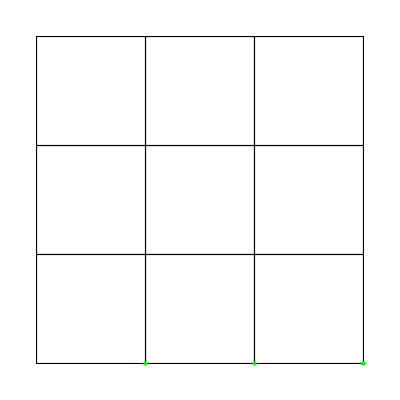

{0.131258,Null}

```mathematica
abt = Block[{MaxCellSize=200,
CrackLen=10,
L=40.0,
RelaxFactor = 0.8,
(*uVec={0.0&,0.2#[[2]]&,0.0&}*)
uVec={0.0&,0.0&,0.0&}
(*,tVec={0.0&,0.0&,0.0&}*)
,tVec={0.0&,5.0&,0.0&}
,TracInd
(*,MaterialProperty,NMat,dN,GuassPointsNatural,GuassWeights,ngauss,Coords,IEN,nnp,nen,nel,ndof,IENS,nsen,nsel,𝕀0,ℐ
,DirichletPoints,DirichletDof,NeumannPoints,NeumannDof,Edges,DirichletVals,NeumannVals,IDMat,IDno*)
(*,Fd,UMat,σ,ϵplas*)
},
TracInd=Norm@Through[tVec[1,1,1]]>10^-5;
(*Coords={{0.,0.},{0.,0.5},{0.,1.},{0.5,0.},{0.5,0.5},{0.5,1.},{1.,0.},{1.,0.5},{1.,1.}};
Connection3={{2,5,6},{6,3,2},{8,9,6},{5,8,6}};
Connection4={{1,4,5,2},{4,7,8,5}};
mesh = ToElementMesh["Coordinates"->Coords
,"MeshElements"->{TriangleElement[Connection3],QuadElement[Connection4]}
,"MeshOrder"->1];*)
mesh=ToElementMesh[Rectangle[{0.0,0.0},{L,L}],MaxCellMeasure->MaxCellSize,"MeshOrder"->1,MeshElementType->QuadElement];
(*mesh=Inp2Mesh@"a1000.inp";*)
MaterialProperty=InitializeFEM[mesh];
DefineBCs[uVec,tVec,L,CrackLen];
Print@PlotMeshBC[DirichletPoints,NeumannPoints,ShowMesh->True,ShowNumbers->False
(*,ShowBCs->"NeumannBC"*)
,ShowBCs->"DirichletBC"
];
(*{Fd,dt}=NewtonSolve[5,1,RelaxFactor,TracInd];*)
(*DumpSave["Apr18_Fd.mx",{Fd,UMat,σ,ϵplas}];*)
]//AbsoluteTiming;
Print[abt]
```

### Post process

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/wenqiangfang/Dropbox (Brown)/Apps/Plasticity_MathematicaCode/Test_Apr22

```mathematica
Get["TestResult.mx"]
```

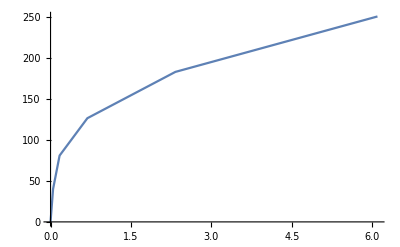

```mathematica
dFERR=PostProcess[Fd[[1,#]],Fd[[2,#]],Fd[[3,#]],dt,40]&/@Range[Length@Fd[[1,;;]]];
ListLinePlot[dFERR[[;;,{1,2}]],PlotRange->All]
```

```mathematica
dFERR[[-1,2]]/40.
```

6.25331

```mathematica
dFERR[[;;,3]]
dFERR[[;;,4]]
dFERR[[;;,5]]
```

{0.,1.88994,9.20283,57.1205,242.092,707.996}

{0.,1.89049,9.29211,60.093,276.505,889.224}

{0.,0.00274099,0.446387,14.8629,172.065,906.141}

### Plot Displacement 2D

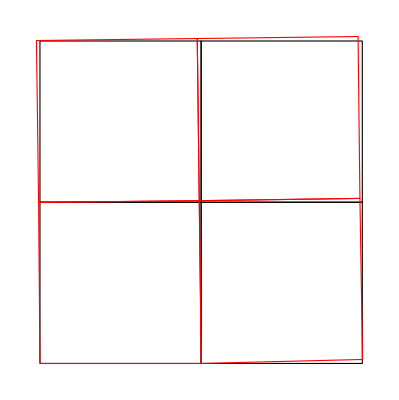

```mathematica
UMat = Fd[[2,-1]];
Ufvec=Table[ElementMeshInterpolation[{mesh}, UMat[[i,;;]]//Normal],{i,1,ndof}];
Show[mesh["Wireframe"],ElementMeshDeformation[mesh,Ufvec,"ScalingFactor"->1]["Wireframe"["MeshElementStyle"->EdgeForm[Red]]]]
```

```mathematica
Ufvec[[2]]@@{1,1}
```

0.005

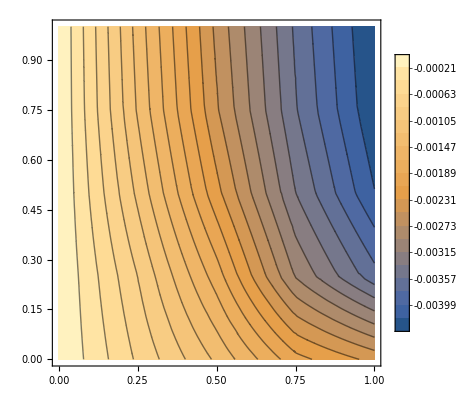

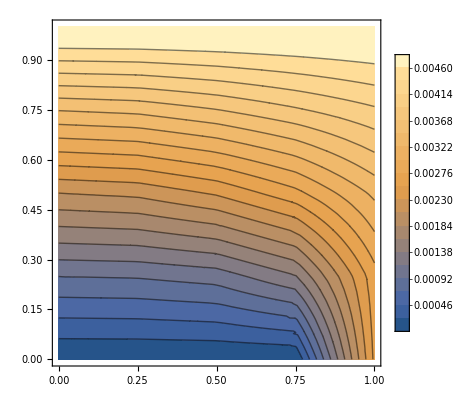

```mathematica
ContourPlot[Ufvec[[1]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[Ufvec[[2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Stress Plot in 2D

```mathematica
ContourPlot[StressMatf[[1,1]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[1,2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[2,2]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
ContourPlot[StressMatf[[3,3]]@@{x1,x2},{x1,x2}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Plot Displacement 3D

```mathematica
SliceContourPlot3D[Ufvec[[1]]@@{x1,x2,x3},Automatic,{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[Ufvec[[2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[Ufvec[[3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```

### Stress Plot in 3D

```mathematica
SliceContourPlot3D[StressMatf[[1,1]]@@{x1,x2,x3},Automatic,{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[2,2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[1,2]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[1,3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
SliceContourPlot3D[StressMatf[[2,3]]@@{x1,x2,x3},"XStackedPlanes",{x1,x2,x3}∈mesh,PlotLegends->Automatic,PlotRange->All,Contours->20]
```